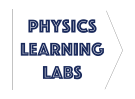
# -Graphics- Prelab 10 - Black Hole Mass

To prepare you for Lab 10, we introduce the concept of a black hole and explore the physical observations of a super massive black hole at the center of the Milky Way. This Prelab develops the framework to allow us to calculate the mass of the black hole in Lab 10.

## Black Hole SgrA*

Despite their exotic properties, black holes consist of the same ordinary matter that composes the Sun, Earth, and all other common elements in the universe. The main characteristic that makes black holes special is that the matter within a black hole is contained within an incredibly small volume. If the mass of the Earth was compressed to a 1 cm diameter sphere, it too would become a black hole!

Observational astronomers have found strong evidence that a massive black hole lies at the center of the Milky Way galaxy. Particularly, in 2001 astronomers were alerted by an unusual source of X-ray emission originating near the southern constellation of Sagittarius (see figure below). The source of this emission was named Sagittarius A* (SgrA*).

Radiation of this wavelength coming from a star was ruled out, and it thus was speculated that the mysterious source of X-ray emission may be a black hole. In order to support this claim, there are two quantities that astronomers may measure near the black hole:

1) The speed of the material orbiting the black hole
  	2) The light emitted near the area of the black hole

The speed yields information about the concentration of mass in the volume of space, while the the light emitted informs us whether the mass could in the form of stars.

### The Observations

Observations of the light emitted from stars near the center of the Milky Way are difficult due to the vast number of stars and dust clouds that obscure our view towards the center. To minimize this problem, astronomers focus on spectrums of light with longer wavelengths that undergo less absorption. In the case of SgrA*, astronomers utilize a near-infrared telescope to image SgrA*. Below is one infrared snapshot - the cross indicates SgrA* while the white circle beneath the cross is a star named S2.

Star S2 is special and is the focus of this Lab 10. The reason is that by tracking and plotting the orbit of star S2 around SgrA*, we can use Kepler’s Laws to infer the mass of SgrA*!

Below is the observational data for star S2 that astronomers have recorded for over 10 years. In Lab 10 we will plot this data directly to find the orbital shape of S2 around SgrA*.

Date | x (arcsec) | dx (arcsec) | y (arcsec) | dy (arcsec)
1992.23 | 0.104 | 0.003 | -0.166 | 0.004
1994.32 | 0.097 | 0.003 | -0.189 | 0.004
1995.53 | 0.087 | 0.002 | -0.192 | 0.003
1996.26 | 0.075 | 0.007 | -0.197 | 0.01
1996.43 | 0.077 | 0.002 | -0.193 | 0.003
1997.54 | 0.052 | 0.004 | -0.183 | 0.006
1998.37 | 0.036 | 0.001 | -0.167 | 0.002
1999.47 | 0.022 | 0.004 | -0.156 | 0.006
2000.47 | 0. | 0.002 | -0.103 | 0.003
2000.52 | -0.013 | 0.003 | -0.113 | 0.004
2001.5 | -0.026 | 0.002 | -0.068 | 0.003
2002.25 | -0.013 | 0.005 | 0.003 | 0.007
2002.33 | -0.007 | 0.003 | 0.016 | 0.004
2002.41 | 0.009 | 0.003 | 0.023 | 0.005
2002.58 | 0.032 | 0.002 | 0.016 | 0.003
2002.65 | 0.037 | 0.002 | 0.009 | 0.003
2003.21 | 0.072 | 0.001 | -0.024 | 0.002
2003.35 | 0.077 | 0.002 | -0.03 | 0.002
2003.45 | 0.081 | 0.002 | -0.036 | 0.002

*The putative black hole is located at (0.0, 0.0)

### Astronomy Units

If you look into the night sky, how can you determine how far away a given star is compared to its neighbor?

You may initially think brighter stars must be closer, but this is not always true. A dim star can just as easily be closer to you than a brighter more distant star. All you can measure with your eye is the angular position of the star. The same is true of the projection of light onto a telescope. Hence, when describing the motion of stars, astronomers use angular distance measurements. If the approximate distance between the Earth and a luminous object is known (via standard candles), then we may use the arclength formula s=rθ to calculate the approximate distances that far away objects move.

Using s=rθ, calculate the arc length (in meters) subtended by the sun when it moves an angular distance of 2 x10^-6 °. The distance between the Earth and Sun is called an AU (astronomical unit). 1 AU = 1.5 x10^11 m. (Don’t forget to convert to radians).

As you can see from the above calculation, a small change in angle can correspond to a large distance. In astronomy angles are typically measured in arcminutes or arcseconds

1 arcmin = 1/60 °
1 arcsec = (1/60) arcmin = 1/(60^2)°

In addition, when discussing distances that are trillions of miles away it is more sensible to units of distance that are on the scale of the solar system, i.e. light years or AU’s.

Light year: the distance traveled by light in one year

Using the speed of light c=3 x 10^8 m/s, convert the distance unit of 1 ly (light year) to meters

Given that SgrA* lies at a distance of 26,000 ly away from Earth, find the distance subtended by star S2 when our telescopes detect that S2 moves 1 arcsec. Remember to convert angles into radians, and express your answer in ld (light days). This ratio of 1 arcsec = __ ld will be needed for calculations in Lab 10.

### Precursors to Lab 10

In Lab 10, we will plot the orbital position of S2 along with error bars given by dx and dy. With this plot, we will use Manipulate find the ellipse of best fit to the data. This will allow us to determine the area A and semi-major axis a of the ellipse.

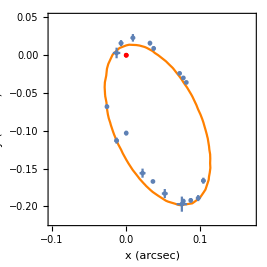

According to the relation dA/dt= A/T, the orbital period T may be determined if we know both the area A and the change in area over time dA/dt. Based on the plot we develop in Lab 10, we will use an approximation method to determine the average dA/dt. Finally, once we have solved for the orbital period T, we may use Kepler’s Law,

T^2 = a^3(4 π^2)/(G(M+m)),

to find the total mass in the denominator (M+m). This gives us the approximate mass of the black hole!

# Submit this completed notebook as a .pdf into HuskyCT. (Make sure all cells sections are visible to receive credit for all your output. As a shortcut, use CTRL+A then CTRL+SHIFT+[ to open all cell sections).